```mathematica
$Assumptions={A1>0,B1>0,A2>0,B2>0,A>0,B>0};

(*A1=A;A2=A;B1=B;B2=B;*)

W1={{-A1-B2,A2+B1 ⅇ^(ⅈ k)},{A1+B2/ⅇ^(ⅈ k),-A2-B1}};
W2={{-A1-B2,A1+B2/ⅇ^(-ⅈ k)},{A2+B1 ⅇ^(-ⅈ k),-A2-B1}};
λ=Eigenvalues[W1];
R=Eigenvectors[W1];
L=Eigenvectors[W2];
R2=Normal[Series[R,{k,0,2}]];
L1[k_]=Normal[Series[L[[1]],{k,0,2}]];
L2[k_]=Normal[Series[L[[2]],{k,0,2}]];

λ2=Normal[Series[λ,{k,0,2}]];
ψ0={1,0};
(*g[k_]=(L2⟦1⟧.ψ0 ⅇ^(t λ2⟦1⟧)+L2⟦2⟧.ψ0 ⅇ^(t λ2⟦2⟧));*)
g[k_]=(L1[-k].ψ0 ⅇ^(t λ2⟦1⟧)+L2[-k].ψ0 ⅇ^(t λ2⟦2⟧));
μ[k_]=-ⅈ D[g[k], {k}];
x2[k_]=-D[D[g[k], {k}], {k}];
(*varX=x2[0]-μ[0]^2;*)
μ[0];
meanX[A1_,A2_,B1_,B2_]=Limit[Coefficient[Normal[Series[μ[0],{t,∞,2}]],t],t->∞]*t+
Limit[Coefficient[Normal[Series[μ[0],{t,∞,2}]],t,0],t->∞];
```

```mathematica
mob[A1_,A2_,B1_,B2_] = Coefficient[meanX[A1,A2,B1,B2],t]
varX[A1_,A2_,B1_,B2_]=FullSimplify[Limit[Coefficient[(x2[0]-(-(B1+B2)/(A1+A2+B1+B2)+((A1 B1-A2 B2) t)/(A1+A2+B1+B2))^2),t],t->∞]]
Diff[A1_,A2_,B1_,B2_]=varX[A1,A2,B1,B2]/2
```

(A1 B1-A2 B2)/(A1+A2+B1+B2)

(A1^3 B1+A2 B2 (A2^2+2 A2 B1+(B1+B2)^2)+A1^2 (2 B1 B2+A2 (2 B1+B2))+A1 (B1 (B1+B2)^2+A2^2 (B1+2 B2)+2 A2 (B1^2+4 B1 B2+B2^2)))/(A1+A2+B1+B2)^3

(A1^3 B1+A2 B2 (A2^2+2 A2 B1+(B1+B2)^2)+A1^2 (2 B1 B2+A2 (2 B1+B2))+A1 (B1 (B1+B2)^2+A2^2 (B1+2 B2)+2 A2 (B1^2+4 B1 B2+B2^2)))/(2 (A1+A2+B1+B2)^3)

```mathematica
A1= a Exp[ s1/2];
A2= a Exp[-  s1/2];
B1=b Exp[ (s2)/2];
B2=b Exp[- (s2)/2];
FullSimplify[Diff[A1,A2,B1,B2]/mob[A1,A2,B1,B2]/Coth[(s1+s2)/2]]
```

(a^2+b^2+a^2 Cosh[s1]+b (b Cosh[s2]+a (2+Cosh[s1]+Cosh[s2]) Sech[(s1+s2)/2]))/(4 (a Cosh[s1/2]+b Cosh[s2/2])^2)

```mathematica
ExpandDenominator[(a^2+b^2+a^2 Cosh[s1]+b (b Cosh[s2]+a (2+Cosh[s1]+Cosh[s2]) Sech[(s1+s2)/2]))/(4 (a Cosh[s1/2]+b Cosh[s2/2])^2)]
```

```mathematica
FullSimplify[(a^2+b^2+a^2 Cosh[s1]+b (b Cosh[s2]+a (2+Cosh[s1]+Cosh[s2]) Sech[(s1+s2)/2]))/(4 a^2 Cosh[s1/2]^2+8 a b Cosh[s1/2] Cosh[s2/2]+4 b^2 Cosh[s2/2]^2)]
```

```mathematica
FullSimplify[(a^2+b^2+a^2 Cosh[s1]+b^2 Cosh[s2]+a b (2+Cosh[s1]+Cosh[s2]) Sech[(s1+s2)/2])/(4 (a Cosh[s1/2]+b Cosh[s2/2])^2)/(a b )]
```

(a^2+b^2+a^2 Cosh[s1]+b^2 Cosh[s2]+a b (2+Cosh[s1]+Cosh[s2]) Sech[(s1+s2)/2])/(4 a b (a Cosh[s1/2]+b Cosh[s2/2])^2)

```mathematica
(a^2+b^2+a^2 Cosh[s1]+b (b Cosh[s2]+a (2+Cosh[s1]+Cosh[s2])  Sech[(s1+s2)/2]))/(4 a^2 Cosh[s1/2]^2+8 a b Cosh[s1/2] Cosh[s2/2]+4 b^2 Cosh[s2/2]^2)
```

```mathematica
TrigExpand[(a^2+b^2+a^2 Cosh[s1]+b (b Cosh[s2]+a (2+Cosh[s1]+Cosh[s2]) Sech[(s1+s2)/2]))/(4 (a Cosh[s1/2]+b Cosh[s2/2])^2)]
```

a^2/(4 (a Cosh[s1/2]+b Cosh[s2/2])^2)+b^2/(4 (a Cosh[s1/2]+b Cosh[s2/2])^2)+(a^2 Cosh[s1/2]^2)/(4 (a Cosh[s1/2]+b Cosh[s2/2])^2)+(b^2 Cosh[s2/2]^2)/(4 (a Cosh[s1/2]+b Cosh[s2/2])^2)+(a^2 Sinh[s1/2]^2)/(4 (a Cosh[s1/2]+b Cosh[s2/2])^2)+(b^2 Sinh[s2/2]^2)/(4 (a Cosh[s1/2]+b Cosh[s2/2])^2)+(a b)/(2 (a Cosh[s1/2]+b Cosh[s2/2])^2 (Cosh[s1/2] Cosh[s2/2]+Sinh[s1/2] Sinh[s2/2]))+(a b Cosh[s1/2]^2)/(4 (a Cosh[s1/2]+b Cosh[s2/2])^2 (Cosh[s1/2] Cosh[s2/2]+Sinh[s1/2] Sinh[s2/2]))+(a b Cosh[s2/2]^2)/(4 (a Cosh[s1/2]+b Cosh[s2/2])^2 (Cosh[s1/2] Cosh[s2/2]+Sinh[s1/2] Sinh[s2/2]))+(a b Sinh[s1/2]^2)/(4 (a Cosh[s1/2]+b Cosh[s2/2])^2 (Cosh[s1/2] Cosh[s2/2]+Sinh[s1/2] Sinh[s2/2]))+(a b Sinh[s2/2]^2)/(4 (a Cosh[s1/2]+b Cosh[s2/2])^2 (Cosh[s1/2] Cosh[s2/2]+Sinh[s1/2] Sinh[s2/2]))

```mathematica
TrigToExp[(a^2+b^2+a^2 Cosh[s1]+b (b Cosh[s2]+a (2+Cosh[s1]+Cosh[s2]) Sech[(s1+s2)/2]))/(4 (a Cosh[s1/2]+b Cosh[s2/2])^2)]
```

(a^2+b^2+1/2 a^2 (ⅇ^-s1+ⅇ^s1)+b (1/2 b (ⅇ^-s2+ⅇ^s2)+(2 a (2+1/2 (ⅇ^-s1+ⅇ^s1)+1/2 (ⅇ^-s2+ⅇ^s2)))/(ⅇ^(1/2 (-s1-s2))+ⅇ^((s1+s2)/2))))/(4 (1/2 a (ⅇ^(-s1/2)+ⅇ^(s1/2))+1/2 b (ⅇ^(-s2/2)+ⅇ^(s2/2)))^2)

```mathematica
ExpToTrig[(a^2+b^2+1/2 a^2 (ⅇ^-s1+ⅇ^s1)+b (1/2 b (ⅇ^-s2+ⅇ^s2)+(2 a (2+1/2 (ⅇ^-s1+ⅇ^s1)+1/2 (ⅇ^-s2+ⅇ^s2)))/(ⅇ^(1/2 (-s1-s2))+ⅇ^((s1+s2)/2))))/(4 (1/2 a (ⅇ^(-s1/2)+ⅇ^(s1/2))+1/2 b (ⅇ^(-s2/2)+ⅇ^(s2/2)))^2)]
```

(a^2+b^2+a^2 Cosh[s1]+b (b Cosh[s2]+(2 a (2+Cosh[s1]+Cosh[s2]))/(Cosh[s1/2+s2/2]+Cosh[(s1+s2)/2]-Sinh[s1/2+s2/2]+Sinh[(s1+s2)/2])))/(4 (a Cosh[s1/2]+b Cosh[s2/2])^2)

```mathematica
Sec[0]
```

1

```mathematica
FullSimplify[%24]
```

(a b (a^2 ⅇ^s2 (1+ⅇ^s1)^2 (1+ⅇ^(s1+s2))+b^2 ⅇ^s1 (1+ⅇ^s2)^2 (1+ⅇ^(s1+s2))+4 a b ⅇ^((3 (s1+s2))/2) (2+Cosh[s1]+Cosh[s2])))/(2 (a ⅇ^(s2/2) (1+ⅇ^s1)+b ⅇ^(s1/2) (1+ⅇ^s2))^3)

```mathematica
varX[A1,A2,A1,A2]/2
```

(A1^4+A2^2 (2 A1 A2+A2^2+(A1+A2)^2)+A1^2 (2 A1 A2+A2 (2 A1+A2))+A1 (A1 (A1+A2)^2+A2^2 (A1+2 A2)+2 A2 (A1^2+4 A1 A2+A2^2)))/(2 (2 A1+2 A2)^3)

```mathematica
FullSimplify[μ[A1,A2,A1,A2]/Diff[A1,A2,A1,A2]]
```

4 Tanh[s/2]

```mathematica
FullSimplify[%63]
```

(2 (a+b)^2 Sinh[s])/(2 a b+(a^2+b^2) Cosh[s])

```mathematica
Simplify[(A1^4+A2^2 (2 A1 A2+A2^2+(A1+A2)^2)+A1^2 (2 A1 A2+A2 (2 A1+A2))+A1 (A1 (A1+A2)^2+A2^2 (A1+2 A2)+2 A2 (A1^2+4 A1 A2+A2^2)))/(2 (2 A1+2 A2)^3)]
```

(A1+A2)/8

```mathematica
ExpandNumerator[(A1^3 B1+A2 B2 (A2^2+2 A2 B1+(B1+B2)^2)+A1^2 (2 B1 B2+A2 (2 B1+B2))+A1 (B1 (B1+B2)^2+A2^2 (B1+2 B2)+2 A2 (B1^2+4 B1 B2+B2^2)))/(A1+A2+B1+B2)^3]
```

1/(A1+A2+B1+B2)^3(A1^3 B1+2 A1^2 A2 B1+A1 A2^2 B1+2 A1 A2 B1^2+A1 B1^3+A1^2 A2 B2+2 A1 A2^2 B2+A2^3 B2+2 A1^2 B1 B2+8 A1 A2 B1 B2+2 A2^2 B1 B2+2 A1 B1^2 B2+A2 B1^2 B2+2 A1 A2 B2^2+A1 B1 B2^2+2 A2 B1 B2^2+A2 B2^3)

```mathematica
ExpandNumerator[(A1^4+A2^2 (2 A1 A2+A2^2+(A1+A2)^2)+A1^2 (2 A1 A2+A2 (2 A1+A2))+A1 (A1 (A1+A2)^2+A2^2 (A1+2 A2)+2 A2 (A1^2+4 A1 A2+A2^2)))/(2 A1+2 A2)^3]
```

(2 A1^4+8 A1^3 A2+12 A1^2 A2^2+8 A1 A2^3+2 A2^4)/(2 A1+2 A2)^3

(-ⅇ^-s+ⅇ^s)/(2 ⅇ^(-s/2)+2 ⅇ^(s/2))

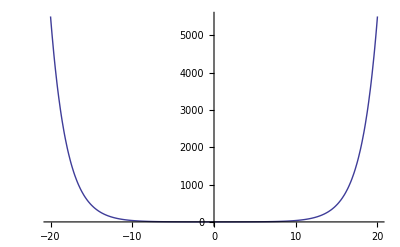

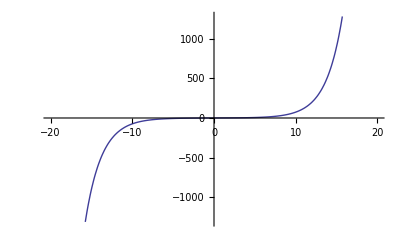

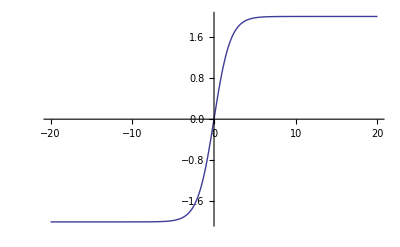

```mathematica
A1=A*Exp[s/2];
A2 = A*Exp[-s/2];
B1=B*Exp[(s)/2];
B2 = B*Exp[-(s)/2];
A=1;
B=10;
mob[A1_,A2_,B1_,B2_] = Coefficient[meanX[A1,A2,B1,B2],t]
Plot[varX[A1,A2,B1,B2],{s,-20,20},PlotRange->Full]
Plot[mob[A1,A2,B1,B2],{s,-20,20}]
Plot[mob[A1,A2,B1,B2]/varX[A1,A2,B1,B2],{s,-20,20},PlotRange->Full]
```

```mathematica
Diff[A1,A2,B1,B2]
```

(A1^3 B1+A2 B2 (A2^2+2 A2 B1+(B1+B2)^2)+A1^2 (2 B1 B2+A2 (2 B1+B2))+A1 (B1 (B1+B2)^2+A2^2 (B1+2 B2)+2 A2 (B1^2+4 B1 B2+B2^2)))/(A1+A2+B1+B2)^3

```mathematica
ExpandNumerator[(A1^3 B1+A2 B2 (A2^2+2 A2 B1+(B1+B2)^2)+A1^2 (2 B1 B2+A2 (2 B1+B2))+A1 (B1 (B1+B2)^2+A2^2 (B1+2 B2)+2 A2 (B1^2+4 B1 B2+B2^2)))/(A1+A2+B1+B2)^3]
```

1/(A1+A2+B1+B2)^3(A1^3 B1+2 A1^2 A2 B1+A1 A2^2 B1+2 A1 A2 B1^2+A1 B1^3+A1^2 A2 B2+2 A1 A2^2 B2+A2^3 B2+2 A1^2 B1 B2+8 A1 A2 B1 B2+2 A2^2 B1 B2+2 A1 B1^2 B2+A2 B1^2 B2+2 A1 A2 B2^2+A1 B1 B2^2+2 A2 B1 B2^2+A2 B2^3)

```mathematica
ExpandNumerator[1/(A1+A2+B1+B2)^3(A1^3 B1+A2 B2 (A2^2+2 A2 B1+(B1+B2)^2)+A1^2 (2 B1 B2+A2 (2 B1+B2))+A1 (B1 (B1+B2)^2+A2^2 (B1+2 B2)+2 A2 (B1^2+4 B1 B2+B2^2))-4((A1+A2)^3(B1+B2)+(A1+A2)(B1+B2)^3)/2)]
```

1/(A1+A2+B1+B2)^3(-A1^3 B1-4 A1^2 A2 B1-5 A1 A2^2 B1-2 A2^3 B1+2 A1 A2 B1^2-A1 B1^3-2 A2 B1^3-2 A1^3 B2-5 A1^2 A2 B2-4 A1 A2^2 B2-A2^3 B2+2 A1^2 B1 B2+8 A1 A2 B1 B2+2 A2^2 B1 B2-4 A1 B1^2 B2-5 A2 B1^2 B2+2 A1 A2 B2^2-5 A1 B1 B2^2-4 A2 B1 B2^2-2 A1 B2^3-A2 B2^3)

```mathematica
Simplify[%53]
```

-1/(A1+A2+B1+B2)^3(A1^3 (B1+2 B2)+A1^2 (4 A2 B1+5 A2 B2-2 B1 B2)+A2 (-2 A2 B1 B2+A2^2 (2 B1+B2)+(B1+B2)^2 (2 B1+B2))+A1 ((B1+B2)^2 (B1+2 B2)+A2^2 (5 B1+4 B2)-2 A2 (B1^2+4 B1 B2+B2^2)))

```mathematica
Simplify[%51]
```

1/(2 (A1+A2+B1+B2)^3)(A1^3 (B1-B2)+A1^2 (A2 (B1-B2)+4 B1 B2)+A2 (4 A2 B1 B2+A2^2 (-B1+B2)-(B1-B2) (B1+B2)^2)+A1 (A2^2 (-B1+B2)+(B1-B2) (B1+B2)^2+4 A2 (B1^2+4 B1 B2+B2^2)))

```mathematica
Simplify[%48]
```

-(A1^3 B2+A2 B1 (A2^2-2 A2 B2+(B1+B2)^2)+A1^2 (-2 B1 B2+A2 (B1+2 B2))+A1 (B2 (B1+B2)^2+A2^2 (2 B1+B2)-2 A2 (B1^2+4 B1 B2+B2^2)))/(A1+A2+B1+B2)^3

```mathematica
Simplify[%45]
```

1/(A1+A2+B1+B2)^3(-A1^3 B2+A1^2 (2 B1 B2-A2 (B1+2 B2))+A2 (-A2^2 B1+2 A2 B1 B2+(B1+B2)^2 (B1+2 B2))+A1 (-A2^2 (2 B1+B2)+(B1+B2)^2 (2 B1+B2)+2 A2 (B1^2+4 B1 B2+B2^2)))

```mathematica
ExpandNumerator[(A1^4+A2^2 (2 A1 A2+A2^2+(A1+A2)^2)+A1^2 (2 A1 A2+A2 (2 A1+A2))+A1 (A1 (A1+A2)^2+A2^2 (A1+2 A2)+2 A2 (A1^2+4 A1 A2+A2^2)))/(2 A1+2 A2)^3]
```

(2 A1^4+8 A1^3 A2+12 A1^2 A2^2+8 A1 A2^3+2 A2^4)/(2 A1+2 A2)^3

```mathematica
(A1+A2)^2*(B1+B2)
```

(A1+A2)^2 (B1+B2)

```mathematica
Expand[(A1+A2)^3(B1+B2)+(A1+A2)(B1+B2)^3-(A1+A2)^2(B1+B2)^2]
```

A1^3 B1+3 A1^2 A2 B1+3 A1 A2^2 B1+A2^3 B1-A1^2 B1^2-2 A1 A2 B1^2-A2^2 B1^2+A1 B1^3+A2 B1^3+A1^3 B2+3 A1^2 A2 B2+3 A1 A2^2 B2+A2^3 B2-2 A1^2 B1 B2-4 A1 A2 B1 B2-2 A2^2 B1 B2+3 A1 B1^2 B2+3 A2 B1^2 B2-A1^2 B2^2-2 A1 A2 B2^2-A2^2 B2^2+3 A1 B1 B2^2+3 A2 B1 B2^2+A1 B2^3+A2 B2^3

```mathematica
Simplify[%42]
```

(A1+A2) (B1+B2) (A1^2+A2^2+A1 (2 A2-B1-B2)-A2 (B1+B2)+(B1+B2)^2)

```mathematica
Expand[(A1+A2)^2 (B1+B2)^2]
```

A1^2 B1^2+2 A1 A2 B1^2+A2^2 B1^2+2 A1^2 B1 B2+4 A1 A2 B1 B2+2 A2^2 B1 B2+A1^2 B2^2+2 A1 A2 B2^2+A2^2 B2^2

```mathematica
Expand[(A1+A2)^4]
```

A1^4+4 A1^3 A2+6 A1^2 A2^2+4 A1 A2^3+A2^4

```mathematica
Simplify[(A1^4+A2^2 (2 A1 A2+A2^2+(A1+A2)^2)+A1^2 (2 A1 A2+A2 (2 A1+A2))+A1 (A1 (A1+A2)^2+A2^2 (A1+2 A2)+2 A2 (A1^2+4 A1 A2+A2^2)))/(2 A1+2 A2)^3]
```

(A1+A2)/4

```mathematica
Simplify[1/(A1+A2+B1+B2)^3(A1^3 B1+A2 B2 (A2^2+2 A2 B1+(B1+B2)^2)+A1^2 (2 B1 B2+A2 (2 B1+B2))+A1 (B1 (B1+B2)^2+A2^2 (B1+2 B2)+2 A2 (B1^2+4 B1 B2+B2^2)))]
```

1/(A1+A2+B1+B2)^3(A1^3 B1+A2 B2 (A2^2+2 A2 B1+(B1+B2)^2)+A1^2 (2 B1 B2+A2 (2 B1+B2))+A1 (B1 (B1+B2)^2+A2^2 (B1+2 B2)+2 A2 (B1^2+4 B1 B2+B2^2)))

```mathematica
Simplify[1/(2 A1+2 A2)^3(A1^4+A2^2 (2 A1 A2+A2^2+(A1+A2)^2)+A1^2 (2 A1 A2+A2 (2 A1+A2))+A1 (A1 (A1+A2)^2+A2^2 (A1+2 A2)+2 A2 (A1^2+4 A1 A2+A2^2)))]
```

(A1+A2)/4

```mathematica
mob[A1,A2,A1,A2]
```

(A1^2-A2^2)/(2 A1+2 A2)

```mathematica
A1*A2*2/(A1+A2+A1+A2)
```

(2 A1 A2)/(2 A1+2 A2)

```mathematica
Diff[A,A,B,B]
```

(A^3 B+A^2 (3 A B+2 B^2)+A B (A^2+2 A B+4 B^2)+A (3 A^2 B+12 A B^2+4 B^3))/(2 A+2 B)^3

```mathematica
Simplify[(A^3 B+A^2 (3 A B+2 B^2)+A B (A^2+2 A B+4 B^2)+A (3 A^2 B+12 A B^2+4 B^3))/(2 A+2 B)^3]
```

(A B)/(A+B)

```mathematica
Diff[A1,A2,B1,B2]
```

(A1^3 B1+A2 B2 (A2^2+2 A2 B1+(B1+B2)^2)+A1^2 (2 B1 B2+A2 (2 B1+B2))+A1 (B1 (B1+B2)^2+A2^2 (B1+2 B2)+2 A2 (B1^2+4 B1 B2+B2^2)))/(A1+A2+B1+B2)^3

```mathematica
Simplify[(A1^4+A2^2 (2 A1 A2+A2^2+(A1+A2)^2)+A1^2 (2 A1 A2+A2 (2 A1+A2))+A1 (A1 (A1+A2)^2+A2^2 (A1+2 A2)+2 A2 (A1^2+4 A1 A2+A2^2)))/(2 A1+2 A2)^3]
```

(A1+A2)/4

```mathematica
varX[A1,A2,B1,B2]-Diff[A1,A2,B1,B2]/4
```

(7 (A1^3 B1+A2 B2 (A2^2+2 A2 B1+(B1+B2)^2)+A1^2 (2 B1 B2+A2 (2 B1+B2))+A1 (B1 (B1+B2)^2+A2^2 (B1+2 B2)+2 A2 (B1^2+4 B1 B2+B2^2))))/(8 (A1+A2+B1+B2)^3)

```mathematica
Simplify[-(3 (A1^3 B1+A2 B2 (A2^2+2 A2 B1+(B1+B2)^2)+A1^2 (2 B1 B2+A2 (2 B1+B2))+A1 (B1 (B1+B2)^2+A2^2 (B1+2 B2)+2 A2 (B1^2+4 B1 B2+B2^2))))/(A1+A2+B1+B2)^3]
```

-(3 (A1^3 B1+A2 B2 (A2^2+2 A2 B1+(B1+B2)^2)+A1^2 (2 B1 B2+A2 (2 B1+B2))+A1 (B1 (B1+B2)^2+A2^2 (B1+2 B2)+2 A2 (B1^2+4 B1 B2+B2^2))))/(A1+A2+B1+B2)^3

```mathematica
Simplify[(3 (A1^3 B1+A2 B2 (A2^2+2 A2 B1+(B1+B2)^2)+A1^2 (2 B1 B2+A2 (2 B1+B2))+A1 (B1 (B1+B2)^2+A2^2 (B1+2 B2)+2 A2 (B1^2+4 B1 B2+B2^2))))/(A1+A2+B1+B2)^3]
```

(3 (A1^3 B1+A2 B2 (A2^2+2 A2 B1+(B1+B2)^2)+A1^2 (2 B1 B2+A2 (2 B1+B2))+A1 (B1 (B1+B2)^2+A2^2 (B1+2 B2)+2 A2 (B1^2+4 B1 B2+B2^2))))/(A1+A2+B1+B2)^3

```mathematica
Simplify[(A1^3 B1+A2 B2 (A2^2+2 A2 B1+(B1+B2)^2)+A1^2 (2 B1 B2+A2 (2 B1+B2))+A1 (B1 (B1+B2)^2+A2^2 (B1+2 B2)+2 A2 (B1^2+4 B1 B2+B2^2)))/(A1+A2+B1+B2)^3]
```

(A1^3 B1+A2 B2 (A2^2+2 A2 B1+(B1+B2)^2)+A1^2 (2 B1 B2+A2 (2 B1+B2))+A1 (B1 (B1+B2)^2+A2^2 (B1+2 B2)+2 A2 (B1^2+4 B1 B2+B2^2)))/(A1+A2+B1+B2)^3

```mathematica
Simplify[-(A1^3 B1+A2 B2 (A2^2+2 A2 B1+(B1+B2)^2)+A1^2 (2 B1 B2+A2 (2 B1+B2))+A1 (B1 (B1+B2)^2+A2^2 (B1+2 B2)+2 A2 (B1^2+4 B1 B2+B2^2)))/(2 (A1+A2+B1+B2)^3)]
```

-(A1^3 B1+A2 B2 (A2^2+2 A2 B1+(B1+B2)^2)+A1^2 (2 B1 B2+A2 (2 B1+B2))+A1 (B1 (B1+B2)^2+A2^2 (B1+2 B2)+2 A2 (B1^2+4 B1 B2+B2^2)))/(2 (A1+A2+B1+B2)^3)

```mathematica
Diff[A1,A2,B1,B1]-(4*(A1*A2+B1*B2)-mob[A1,A2,B1,B2]^2)/(A1+A2+B1+B2)
```

(A1^3 B1+A1^2 (3 A2 B1+2 B1^2)+A2 B1 (A2^2+2 A2 B1+4 B1^2)+A1 (3 A2^2 B1+12 A2 B1^2+4 B1^3))/(2 (A1+A2+2 B1)^3)-(-(4 (A1 B1-A2 B2)^2)/(A1+A2+B1+B2)^2+4 (A1 A2+B1 B2))/(A1+A2+B1+B2)

```mathematica
FullSimplify[(A1^3 B1+A1^2 (3 A2 B1+2 B1^2)+A2 B1 (A2^2+2 A2 B1+4 B1^2)+A1 (3 A2^2 B1+12 A2 B1^2+4 B1^3))/(2 (A1+A2+2 B1)^3)-(-(4 (A1 B1-A2 B2)^2)/(A1+A2+B1+B2)^2+4 (A1 A2+B1 B2))/(A1+A2+B1+B2)]
```

(B1 ((A1+A2)^3+2 (A1^2+6 A1 A2+A2^2) B1+4 (A1+A2) B1^2))/(2 (A1+A2+2 B1)^3)-(4 (A1 A2+B1 B2-(A1 B1-A2 B2)^2/(A1+A2+B1+B2)^2))/(A1+A2+B1+B2)

```mathematica
Simplify[(A1^3 B1+A1^2 (3 A2 B1+2 B1^2)+A2 B1 (A2^2+2 A2 B1+4 B1^2)+A1 (3 A2^2 B1+12 A2 B1^2+4 B1^3))/(2 (A1+A2+2 B1)^3)-(-(4 (A1 B1-A2 B2)^2)/(A1+A2+B1+B2)^2+2 (A1 A2+B1 B2))/(A1+A2+B1+B2)]
```

(B1 (A1^3+A1^2 (3 A2+2 B1)+A2 (A2^2+2 A2 B1+4 B1^2)+A1 (3 A2^2+12 A2 B1+4 B1^2)))/(2 (A1+A2+2 B1)^3)-(2 (A1 A2+B1 B2-(2 (A1 B1-A2 B2)^2)/(A1+A2+B1+B2)^2))/(A1+A2+B1+B2)

```mathematica
Expand[(B1 (A1^3+A1^2 (3 A2+2 B1)+A2 (A2^2+2 A2 B1+4 B1^2)+A1 (3 A2^2+12 A2 B1+4 B1^2)))/(2 (A1+A2+2 B1)^3)-(2 (A1 A2+B1 B2-(2 (A1 B1-A2 B2)^2)/(A1+A2+B1+B2)^2))/(A1+A2+B1+B2)]
```

(A1^3 B1)/(2 (A1+A2+2 B1)^3)+(3 A1^2 A2 B1)/(2 (A1+A2+2 B1)^3)+(3 A1 A2^2 B1)/(2 (A1+A2+2 B1)^3)+(A2^3 B1)/(2 (A1+A2+2 B1)^3)+(A1^2 B1^2)/(A1+A2+2 B1)^3+(6 A1 A2 B1^2)/(A1+A2+2 B1)^3+(A2^2 B1^2)/(A1+A2+2 B1)^3+(2 A1 B1^3)/(A1+A2+2 B1)^3+(2 A2 B1^3)/(A1+A2+2 B1)^3+(4 A1^2 B1^2)/(A1+A2+B1+B2)^3-(8 A1 A2 B1 B2)/(A1+A2+B1+B2)^3+(4 A2^2 B2^2)/(A1+A2+B1+B2)^3-(2 A1 A2)/(A1+A2+B1+B2)-(2 B1 B2)/(A1+A2+B1+B2)

```mathematica
Simplify[%127]
```

1/2 ((A1^3 B1)/(A1+A2+2 B1)^3+(A2^3 B1)/(A1+A2+2 B1)^3+(4 A2 B1^3)/(A1+A2+2 B1)^3-(4 B1 B2)/(A1+A2+B1+B2)+A2^2 ((2 B1^2)/(A1+A2+2 B1)^3+(8 B2^2)/(A1+A2+B1+B2)^3)+A1^2 B1 ((3 A2)/(A1+A2+2 B1)^3+2 B1 (1/(A1+A2+2 B1)^3+4/(A1+A2+B1+B2)^3))+A1 ((3 A2^2 B1)/(A1+A2+2 B1)^3+(4 B1^3)/(A1+A2+2 B1)^3+A2 ((12 B1^2)/(A1+A2+2 B1)^3-(16 B1 B2)/(A1+A2+B1+B2)^3-4/(A1+A2+B1+B2))))

```mathematica
Simplify[(2 (A1^3 B1+A1^2 (3 A2 B1+2 B1^2)+A2 B1 (A2^2+2 A2 B1+4 B1^2)+A1 (3 A2^2 B1+12 A2 B1^2+4 B1^3)))/(A1+A2+2 B1)^3-(-(A1 B1-A2 B2)^2/(A1+A2+B1+B2)^2+2 (A1 A2+B1 B2))/(A1+A2+B1+B2)]
```

(2 B1 (A1^3+A1^2 (3 A2+2 B1)+A2 (A2^2+2 A2 B1+4 B1^2)+A1 (3 A2^2+12 A2 B1+4 B1^2)))/(A1+A2+2 B1)^3-(-(A1 B1-A2 B2)^2/(A1+A2+B1+B2)^2+2 (A1 A2+B1 B2))/(A1+A2+B1+B2)

```mathematica
Simplify[(A1^3 B1+A1^2 (3 A2 B1+2 B1^2)+A2 B1 (A2^2+2 A2 B1+4 B1^2)+A1 (3 A2^2 B1+12 A2 B1^2+4 B1^3))/(A1+A2+2 B1)^3-(-(A1 B1-A2 B2)^2/(A1+A2+B1+B2)^2+2 (A1 A2+B1 B2))/(A1+A2+B1+B2)]
```

(B1 (A1^3+A1^2 (3 A2+2 B1)+A2 (A2^2+2 A2 B1+4 B1^2)+A1 (3 A2^2+12 A2 B1+4 B1^2)))/(A1+A2+2 B1)^3-(-(A1 B1-A2 B2)^2/(A1+A2+B1+B2)^2+2 (A1 A2+B1 B2))/(A1+A2+B1+B2)

```mathematica
m[A1_,A2_,B1_,B2_]=2*(A1*B1-A2*B2)/(A1+A2+B1+B2)
d[A1_,A2_,B1_,B2_]=(2*(A1*B1+A2*B2)-m[A1,A2,B1,B2]^2)/(A1+A2+B1+B2)
```

(2 (A1 B1-A2 B2))/(A1+A2+B1+B2)

(-(4 (A1 B1-A2 B2)^2)/(A1+A2+B1+B2)^2+2 (A1 B1+A2 B2))/(A1+A2+B1+B2)

```mathematica
m[A1,A2,B1,B2]/d[A1,A2,B1,B2]
```

(2 (A1 B1-A2 B2))/(-(4 (A1 B1-A2 B2)^2)/(A1+A2+B1+B2)^2+2 (A1 B1+A2 B2))

```mathematica
A1=Exp[α*s];
A2=1;
B1=Exp[(1-α)s];
B2=1;
Expand[FullSimplify[ExpandDenominator[ExpandNumerator[(2 (A1 B1-A2 B2))/(-(4 (A1 B1-A2 B2)^2)/(A1+A2+B1+B2)^2+2 (A1 B1+A2 B2))]]]]
```

-4/(2+ⅇ^(s/3) (4+5 ⅇ^(s/3)+10 ⅇ^(2 s/3)+5 ⅇ^s+5 ⅇ^(4 s/3)+ⅇ^(2 s)))-(4 ⅇ^(s/3))/(2+ⅇ^(s/3) (4+5 ⅇ^(s/3)+10 ⅇ^(2 s/3)+5 ⅇ^s+5 ⅇ^(4 s/3)+ⅇ^(2 s)))-(5 ⅇ^(2 s/3))/(2+ⅇ^(s/3) (4+5 ⅇ^(s/3)+10 ⅇ^(2 s/3)+5 ⅇ^s+5 ⅇ^(4 s/3)+ⅇ^(2 s)))+(2 ⅇ^s)/(2+ⅇ^(s/3) (4+5 ⅇ^(s/3)+10 ⅇ^(2 s/3)+5 ⅇ^s+5 ⅇ^(4 s/3)+ⅇ^(2 s)))+(3 ⅇ^(4 s/3))/(2+ⅇ^(s/3) (4+5 ⅇ^(s/3)+10 ⅇ^(2 s/3)+5 ⅇ^s+5 ⅇ^(4 s/3)+ⅇ^(2 s)))+(5 ⅇ^(5 s/3))/(2+ⅇ^(s/3) (4+5 ⅇ^(s/3)+10 ⅇ^(2 s/3)+5 ⅇ^s+5 ⅇ^(4 s/3)+ⅇ^(2 s)))+(2 ⅇ^(2 s))/(2+ⅇ^(s/3) (4+5 ⅇ^(s/3)+10 ⅇ^(2 s/3)+5 ⅇ^s+5 ⅇ^(4 s/3)+ⅇ^(2 s)))+ⅇ^(7 s/3)/(2+ⅇ^(s/3) (4+5 ⅇ^(s/3)+10 ⅇ^(2 s/3)+5 ⅇ^s+5 ⅇ^(4 s/3)+ⅇ^(2 s)))

```mathematica
α=1/3
FullSimplify[(-1+ⅇ^s)/(1+ⅇ^s-(2 (-1+ⅇ^s)^2)/((2+ⅇ^(s α)+ⅇ^(s-s α))^2))]
```

1/3

```mathematica
(-1+ⅇ^s)/(1+ⅇ^s-(2 (-1+ⅇ^s)^2)/((2+ⅇ^(s/3)+ⅇ^(2 s/3))^2))
```

(-1+ⅇ^s)/(1+ⅇ^s-(2 (-1+ⅇ^s)^2)/((2+ⅇ^(s/3)+ⅇ^(2 s/3))^2))

```mathematica
A1=Exp[α*s];
A2=1;
B1=Exp[(1-α)s];
B2=1;
α=1/3;
r1=m[A1,A2,B1,B2]/d[A1,A2,B1,B2]
```

(2 (-1+ⅇ^s))/(2 (1+ⅇ^s)-(4 (-1+ⅇ^s)^2)/((2+ⅇ^(-s/3)+ⅇ^(4 s/3))^2))

```mathematica
A1=Exp[α*s];
A2=1;
B1=Exp[(1-α)s];
B2=1;
α=4/5;
r2=m[A1,A2,B1,B2]/d[A1,A2,B1,B2]
```

(2 (-1+ⅇ^s))/(2 (1+ⅇ^s)-(4 (-1+ⅇ^s)^2)/((2+ⅇ^(-s/3)+ⅇ^(4 s/3))^2))

```mathematica
r1
```

(2 (-1+ⅇ^s))/(-(4 (-1+ⅇ^s)^2)/((2+ⅇ^(s/3)+ⅇ^(2 s/3))^2)+2 (1+ⅇ^s))

```mathematica
r2
```

(2 (-1+ⅇ^s))/(-(4 (-1+ⅇ^s)^2)/((2+ⅇ^(s/3)+ⅇ^(2 s/3))^2)+2 (1+ⅇ^s))

```mathematica
r1/r2
```

1